# Laboratorium kontrolne

## Jan Czechowski

## Zadanie 1

Statek - współrzędne :

```mathematica
x[t_]:=t
y[t_]:=t^2-1
```

Latarnia - współrzędne:

```mathematica
px:=1
py:=1
```

Odległość statku od latarni

```mathematica
odl[t_]:=√((x[t]-px)^2+(y[t]-py)^2)
```

```mathematica
d[t_]:=(x[t]-px)^2+(y[t]-py)^2
```

```mathematica
d'[t]
```

2 (-1+t)+4 t (-2+t^2)

```mathematica
tMin=Solve[d'[t]==0,t]
```

{{t→-1},{t→1/2 (1-√3)},{t→1/2 (1+√3)}}

Dziedzina to [0, 2]

Jedyną wartością w tym przedziale spośród tMini jest: t→1/2 (1+√3)

```mathematica
tNajmniejsza := 1/2 (1+√3)
xMin=tNajmniejsza;
yMin=y[xMin];
```

Najmniejsza odległość:

```mathematica
NajmniejszaOdl=Simplify[√d[tNajmniejsza]]
```

1/2 √(11-6 √3)

Odp: Najmniejsza odległość to: 1/2 √(11-6 √3)

```mathematica
wspolrzedneStatku ={x[tNajmniejsza],y[tNajmniejsza]}
```

{1/2 (1+√3),-1+1/4 (1+√3)^2}

```mathematica
wektor= wspolrzedneStatku-{px,py}
```

{-1+1/2 (1+√3),-2+1/4 (1+√3)^2}

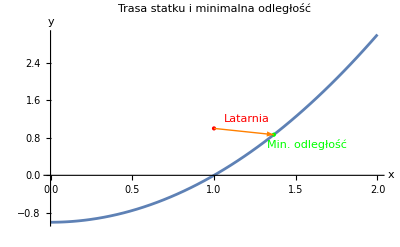

```mathematica
Plot[y[x],{x,0,2},AxesLabel->{"x","y"},PlotLabel->"Trasa statku i minimalna odległość",Epilog->{Red,PointSize[Large],Point[{px,py}],Text["Latarnia",{px+0.2,py+0.2}],Green,PointSize[Large],Point[{xMin,yMin}],Text["Min. odległość",{xMin+0.2,yMin-0.2}],Orange,Arrow[{{px,py},{xMin,yMin}}]}]
```

## Zadanie 2

```mathematica
g[x_]:=Piecewise[{{1-x,0<x<1},{3-2x,1<x<2}}]
```

```mathematica
Plot[g[x],{x,0,2}]
```

Wykres funkcji g(x)

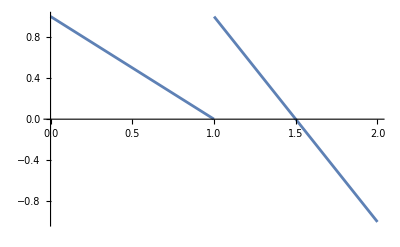

#### a) Przybliżenie samymi sinusami rzędu 9

```mathematica
sin9 = FourierSinSeries[g[x],x,9,FourierParameters->{1,Pi/2}]
```

(4 Sin[(π x)/2])/π^2+Sin[π x]/π-(4 Sin[(3 π x)/2])/(9 π^2)+(3 Sin[2 π x])/(2 π)+(4 Sin[(5 π x)/2])/(25 π^2)+Sin[3 π x]/(3 π)-(4 Sin[(7 π x)/2])/(49 π^2)+(3 Sin[4 π x])/(4 π)+(4 Sin[(9 π x)/2])/(81 π^2)

#### b) Przybliżenie samymi cosinusami rzędu 9

```mathematica
cos9= FourierCosSeries[g[x],x,9,FourierParameters->{1,Pi/2}]
```

1/4-(2 (-6+π) Cos[(π x)/2])/π^2-(2 Cos[π x])/π^2+(2 (2+π) Cos[(3 π x)/2])/(3 π^2)-(2 (-6+5 π) Cos[(5 π x)/2])/(25 π^2)-(2 Cos[3 π x])/(9 π^2)+(2 (6+7 π) Cos[(7 π x)/2])/(49 π^2)+((4-6 π) Cos[(9 π x)/2])/(27 π^2)

```mathematica
Plot[{g[x],sin9,cos9},{x,0,2},PlotLegends->{"g[x]","sin9", "cos9"}]
```

Wykres o którego proszono w poleceniu - funkcji g(x) i jej przybliżeń

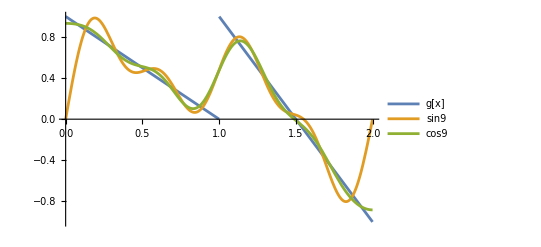

Odp: Lepszym przybliżeniem jest cosinusami rzędu 9, ponieważ lepiej dopasowuje się do funkcji g(x) (np. patrzac na poczatek i koniec wykresu). Wynika to z faktu, że cosinus jest funkcją parzystą, a g(x) ma charakter bardziej parzysty niż nieparzysty.

## Zadanie 3

```mathematica
h[x_,y_]:=x^2+x*y^2-4*x+y^3
```

Pierwsze pochodne:

```mathematica
hx=D[h[x,y],x]
hy=D[h[x,y],y]
```

-4+2 x+y^2

2 x y+3 y^2

Punkty stacjonarne:

```mathematica
Solve[D[h[x,y],x]==0&&D[h[x,y],y]==0]
```

{{x→3/2,y→-1},{x→2,y→0},{x→-6,y→4}}

```mathematica
D[h[x,y],{{x,y},2}]//MatrixForm
```

(2 | 2 y
2 y | 2 x+6 y)

```mathematica
%/.{x->2,y->0}//MatrixForm
```

(2 | 0
0 | 4)

```mathematica
Det[%]
```

8

```mathematica
D[h[x,y],{x,2}]/.{x->2,y->0}
```

2

```mathematica
h[2,0]
```

-4

-4 > 0, więc jest to maksimum lokalne